```mathematica
(*HN3 and HN5Ising AntiFerromagnetic model Renormalization group*)
```

```mathematica
dim=4;
A[3]=B[3]=μ;
```

```mathematica
Z0[x0_,x1_,x2_,x3_,x4_]:=Exp[-A[0]]*A[1]^(-(x0*x1+x1*x2+x2*x3+x3*x4)/4)*A[2]^(-(x0*x2+x2*x4)/4)*μ^(-(x1*x3)/2-y/2(x0*x4))
TrZ0[x0_,x2_,x4_]:=Sum[Sum[Z0[x0,x1,x2,x3,x4],{x1,-1,1,2}],{x3,-1,1,2}]
Z1[x0_,x2_,x4_]:=Exp[-B[0]/2]*B[1]^(-(x0*x2+x2*x4)/4)*B[2]^(-x0*x4/4)
```

```mathematica
i=0;
For[x0=-1,x0≤1,x0+=2,
For[x2=-1,x2≤1,x2+=2,
For[x4=-1,x4≤1,x4+=2,
leq[i]=Z1[x0,x2,x4];
req[i++]=TrZ0[x0,x2,x4];
]
]
]
```

```mathematica
Table[leq[i]==req[i],{i,0,7}];
```

```mathematica
SB[0]=Factor[Simplify[Solve[Factor[leq[0]*leq[1]*leq[2]*leq[1]]==Factor[req[0]*req[1]*req[2]*req[1]],B[0]],A[0]∈Reals&&A[1]∈Reals&&A[2]∈Reals&&C[1]==0]]
SB[1]=Factor[Simplify[Solve[Factor[leq[2]/leq[0]]==Factor[req[2]/req[0]],B[1]],A[0]∈Reals&&A[1]∈Reals&&A[2]∈Reals&&C[1]==0]]
SB[2]=Factor[Simplify[Solve[Factor[leq[1]*leq[1]/leq[0]/leq[2]]==Factor[req[1]*req[1]/req[0]/req[2]],B[2]],A[0]∈Reals&&A[1]∈Reals&&A[2]∈Reals&&C[1]==0]]
(*using Exp[-A[0]], C = Exp[A[0]]*)
```

{{B[0]→1/2 Log[(ⅇ^(4 A[0]) μ^2 A[1]^2)/(2 (1+μ)^3 (1+A[1])^2 (1+2 μ A[1]+A[1]^2))]}}

{{B[1]→(2 (1+μ) A[1] A[2])/(1+2 μ A[1]+A[1]^2)}}

{{B[2]→(μ^(2 y) (1+μ) (1+A[1])^2)/(2 (1+2 μ A[1]+A[1]^2))}}

```mathematica
(* Get the κ(μ) *)
Clear[y]
kap[μ_,κ_,λ_]:=(2 (1+μ) κ *λ)/(1+2 μ *κ+κ^2)
lam[μ_,κ_,λ_]:=(μ^(2 y) (1+μ) (1+κ)^2)/(2 (1+2 μ κ+κ^2))
(kap[μ,κ,λ]/.{λ->(μ^(2 y) (1+μ) (1+κ)^2)/(2 (1+2 μ κ+κ^2))})
Simplify[κfixed=Solve[κ==%,κ]]
Clear[y]
```

(κ (1+κ)^2 μ^(2 y) (1+μ)^2)/((1+κ^2+2 κ μ)^2)

{{κ→0},{κ→1/2 (-2 μ+μ^y+μ^(1+y)-√(4 (-1+μ^y+μ^(1+y))+(-2 μ+μ^y+μ^(1+y))^2))},{κ→1/2 (-2 μ+μ^y+μ^(1+y)+√(4 (-1+μ^y+μ^(1+y))+(-2 μ+μ^y+μ^(1+y))^2))},{κ→1/2 (-2 μ-μ^y-μ^(1+y)-√(-4 (1+μ^y+μ^(1+y))+(2 μ+μ^y+μ^(1+y))^2))},{κ→1/2 (-2 μ-μ^y-μ^(1+y)+√(-4 (1+μ^y+μ^(1+y))+(2 μ+μ^y+μ^(1+y))^2))}}

```mathematica
Simplify[Factor[lam[μ,κ,λ]/.{κ->1/2 (-2 μ-μ^y-μ^(1+y)+√(-4 (1+μ^y+μ^(1+y))+(2 μ+μ^y+μ^(1+y))^2))}]]
```

1/4 μ^y (-2+2 μ+μ^y+μ^(1+y)-√((1+μ) (-4+4 μ-4 μ^y+μ^(2 y)+4 μ^(1+y)+μ^(1+2 y))))

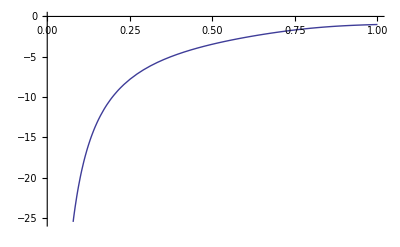

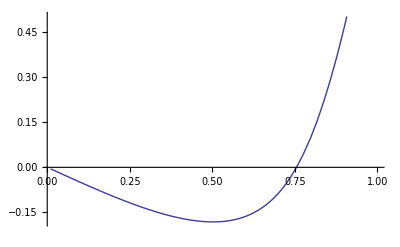

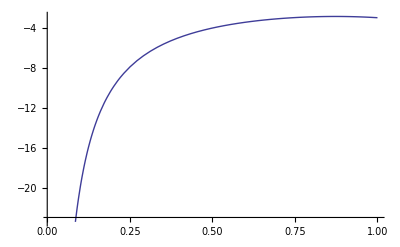

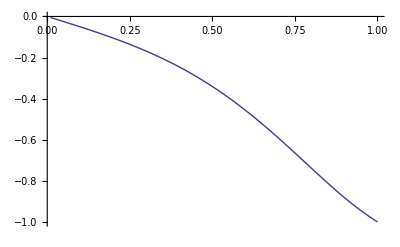

```mathematica
y=-3.0;
Plot[1/2 (-2 μ+μ^y+μ^(1+y)-√(4 (-1+μ^y+μ^(1+y))+(-2 μ+μ^y+μ^(1+y))^2))/.{μ->1/x},{x,0.01,1}]
Plot[1/2 (-2 μ+μ^y+μ^(1+y)+√(4 (-1+μ^y+μ^(1+y))+(-2 μ+μ^y+μ^(1+y))^2))/.{μ->1/x},{x,0.01,1}]
Plot[1/2 (-2 μ-μ^y-μ^(1+y)-√(-4 (1+μ^y+μ^(1+y))+(2 μ+μ^y+μ^(1+y))^2))/.{μ->1/x},{x,0.01,1}]
Plot[1/2 (-2 μ-μ^y-μ^(1+y)+√(-4 (1+μ^y+μ^(1+y))+(2 μ+μ^y+μ^(1+y))^2))/.{μ->1/x},{x,0.01,1}]
Clear[y]
```

The 2nd fixed point is positive or physical; for y<-1.0, there will be a phase transition,
Find the μ_c

```mathematica
y=0.;
Solve[-1+μ^y+μ^(1+y)==0,μ]
NArgMin[{Abs[-1+μ^y+μ^(1+y)],μ>0.0},μ]
Clear[y]
```

{{μ→0.}}

0.

```mathematica
(-2 μ+μ^y+μ^(1+y))^2-4 (-1+μ^y+μ^(1+y))-(-2 μ+μ^y+μ^(1+y))^2
```

-4 (-1+μ^y+μ^(1+y))

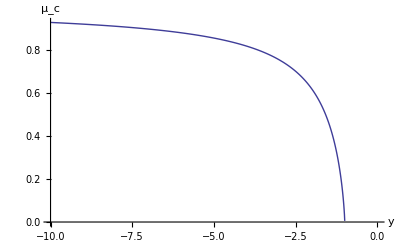

HN35ysFMtrans.csv

```mathematica
Clear[ys]
ys=Range[-10.0,-3.0,0.05];
ys=Join[ys,Range[-2.9,-1.5,0.02]];
ys=Join[ys,Range[-1.49,-1.01,0.01]];
ys=Append[ys,-1.001];
μinvy=ConstantArray[0,Dimensions[ys][[1]]];
For[ind=1,ind≤Dimensions[ys][[1]],ind+=1,y=ys[[ind]];
μinvy[[ind]]=1.0/NArgMin[{Abs[-1+μ^y+μ^(1+y)], μ>=1.0},μ]
]
ListPlot[Table[{ys[[i]],μinvy[[i]]},{i,1,Dimensions[ys][[1]]}],Joined->True,AxesLabel->{"y",μ_c}]
Export["HN35ysFMtrans.csv",Transpose[{ys,μinvy}]]
Clear[ys]
```

```mathematica
Clear[μ,κ,λ]
Factor[lam[μ,κ,λ]/.{κ->1/2 (-2 μ+μ^y+μ^(1+y)+√(4 (-1+μ^y+μ^(1+y))+(-2 μ+μ^y+μ^(1+y))^2))}]
```

1/4 μ^y (2-2 μ+μ^y+μ^(1+y)+√((1+μ) (-4+4 μ+4 μ^y+μ^(2 y)-4 μ^(1+y)+μ^(1+2 y))))

```mathematica
Clear[μ,κ,λ,y]
Jaco=Simplify[Factor[{{D[kap[μ,κ,λ],κ],D[kap[μ,κ,λ],λ]},{D[lam[μ,κ,λ],κ],D[lam[μ,κ,λ],λ]}}]];
Jc=Factor[Eigenvalues[Jaco]];
fixedPoint={κ->1/2 (-2 μ+μ^y+μ^(1+y)+√(4 (-1+μ^y+μ^(1+y))+(-2 μ+μ^y+μ^(1+y))^2)),λ->1/4 μ^y (2-2 μ+μ^y+μ^(1+y)+√((1+μ) (-4+4 μ+4 μ^y+μ^(2 y)-4 μ^(1+y)+μ^(1+2 y))))};
Jev1[μ_]:=-1/((1+κ^2+2 κ μ)^2)(1+μ) (-λ+κ^2 λ+√((-1+κ^2) (-λ^2+κ^2 λ^2-2 κ μ^(2 y)-2 κ^3 μ^(2 y)+2 κ μ^(1+2 y)-4 κ^2 μ^(1+2 y)+2 κ^3 μ^(1+2 y)+4 κ^2 μ^(2+2 y))))/.fixedPoint;
Jev2[μ_]:=-1/((1+κ^2+2 κ μ)^2)(1+μ) (-λ+κ^2 λ-√((-1+κ^2) (-λ^2+κ^2 λ^2-2 κ μ^(2 y)-2 κ^3 μ^(2 y)+2 κ μ^(1+2 y)-4 κ^2 μ^(1+2 y)+2 κ^3 μ^(1+2 y)+4 κ^2 μ^(2+2 y))))/.fixedPoint;
```

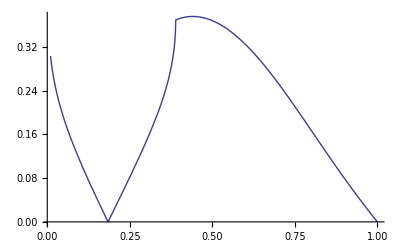

```mathematica
Clear[y,μ,κ,λ]
y=-1.1;
p1=Plot[Abs[Jev1[μ]]/.{μ->1/x},{x,0.01, 1}]
```

```mathematica
Clear[y]
Jaco
```

{{-(2 (-1+κ) (1+κ) λ (1+μ))/((1+κ^2+2 κ μ)^2),(2 κ (1+μ))/(1+κ^2+2 κ μ)},{((-1+κ) (1+κ) (-1+μ) μ^(2 y) (1+μ))/((1+κ^2+2 κ μ)^2),0}}

```mathematica
Clear[κ,λ]
{{D[κ,κ],D[κ,λ]},{D[λ,κ],D[λ,λ]}}
```

{{1,0},{0,1}}